# Arrays and Hypermatrices

## WolframInstitute`Hypergraphs` — the objects of the hypermatrix layer

This notebook shows the array object and the hypermatrix built out of them, together with the design choices behind them. Everything below is live output from src/.

It goes on to the drawing of arrays, the special arrays, the contraction operation ArrayMultiply, the entry-by-entry operations that make arrays multilinear, and the search for equational identities between array operations.

## Loading the package

The cell below is an initialization cell, which the front end evaluates when this notebook is opened. By the time you read this the package is already loaded and every symbol is ready to use; the cell is shown for the record, and needs no running.

```mathematica
PacletDirectoryLoad[ParentDirectory[NotebookDirectory[]]];
Needs["WolframInstitute`Hypergraphs`"]
```

Design note.  PacletInfo.wl in the root of the repository describes the paclet: where its kernel sources are, what context they open, and which symbols belong to it. PacletDirectoryLoad points the kernel at the repository, and Needs then opens the context. Nothing has to be installed, and nothing is copied anywhere — the repository itself is what gets loaded, so an edit to src/ is picked up the next time the notebook is opened.

Design note.  Running PacletDirectoryAdd on the same directory, once, would register it permanently, and then any of the package's symbols would load it on first use in any notebook at all. That writes to the Wolfram user configuration rather than to this repository, so it is left as a choice rather than done here.

## 1. Arrays

An array in the Wolfram Language is a nesting of lists. ArrayObject wraps such a nesting, and that is all it is: one object for every array, whatever its entries are.

```mathematica
ArrayObject[{{1, 2, 3}, {4, 5, 6}}]
```

ArrayObject[…]

It displays as a summary box rather than as its entries, which is what lets an array of any order and any size print in the same amount of space. Normal gives the entries back, and ArrayGraphics draws them:

```mathematica
Normal @ ArrayObject[{{1, 2, 3}, {4, 5, 6}}]
```

{{1,2,3},{4,5,6}}

Design note.  There is one array object rather than one per kind of entry because nothing about the structure of an array depends on what sits in it. The order, the dimensions and the symmetry are the same questions whether the entries are integers, elements of a finite field, generated symbols or labels from a dictionary. An earlier design had a NumericalArray and a SymbolicArray as separate heads; the distinction turned out to buy nothing and cost a slot that was meaningless in each.

### Order and dimensions

The dimensions of an array are the lengths of its indices, and its order is the number of indices. An array of order n is an n-array, so a component vector is a 1-array and a matrix is a 2-array:

```mathematica
arrays = ArrayObject /@ {{1, 2, 3}, {{1, 2}, {3, 4}}, Array[#1 + #2 + #3 &, {2, 2, 2}]};
{ArrayOrder /@ arrays, ArrayDimensions /@ arrays}
```

{{1,2,3},{{3},{2,2},{2,2,2}}}

Dimensions works directly on an array object, as do Normal and the string properties:

```mathematica
m = ArrayObject[{{1, 2, 3}, {4, 5, 6}}];
{Dimensions[m], m["Order"], m["Properties"]}
```

{{2,3},2,{Order,Dimensions,Symmetry,Domain,Entries,RegularQ}}

Design note.  Dimensions and Normal are protected System` symbols, so they are extended with UpValues on the array head rather than redefined. That is the same treatment VertexList and EdgeList get on Hypergraph.

### Regular and irregular

An array is regular when all of its indices range over the same length, and irregular when they do not:

```mathematica
{RegularArrayQ @ ArrayObject[{{1, 2}, {3, 4}}],
  RegularArrayQ @ ArrayObject[{{1, 2, 3}, {4, 5, 6}}]}
```

{True,False}

### Value domains

What an array is made of is not declared: it is asked. ArrayDomain reads the entries and gives the narrowest recognized domain containing every one of them:

```mathematica
ArrayDomain @ ArrayObject[#] & /@ {{True, False}, {1, 2}, {1/2, 3}, {1.5, 2}, {1 + I, 2}}
```

{Boolean,Integer,Rational,Real,Complex}

The elements of a finite field are recognized as that field:

```mathematica
ArrayDomain @ ArrayObject[{FiniteField[2, 1][0], FiniteField[2, 1][1]}]
```

FiniteField[…]

Entries answering to none of them are simply expressions, and make a perfectly good array:

```mathematica
{ArrayDomain @ ArrayObject[{"a", "b"}], ArrayDomain @ ArrayObject[{x, y}],
  ArrayDomain @ ArrayObject[{1, "a"}]}
```

{Expression,Expression,Expression}

Design note.  A computed domain rather than a declared one is what lets the entries be anything. There is nothing to verify and nothing to reject, so an array of labels or of half-built expressions needs no special case: it is an array whose domain happens to be "Expression". "Boolean" means the entries are True and False; entries 0 and 1 are integers, and the two-element field is FiniteField[2, 1] — three different things that all get called boolean in casual use, kept apart here.

## 2. Generated entries

Entries do not have to be given. GenerateSymbolicArray builds them from a name and the indices, and gives back an array like any other:

```mathematica
GenerateSymbolicArray[a, {2, 3}]
```

ArrayObject[…]

```mathematica
Normal @ GenerateSymbolicArray[a, {2, 3}]
```

{{a[1,1],a[1,2],a[1,3]},{a[2,1],a[2,2],a[2,3]}}

Design note.  It is a function, not a kind of object. In that it sits beside ZeroArray, OneArray and IdentityArray, which build their entries from a shape as this one builds them from a name; what comes back from any of them is an ArrayObject. Naming it Generate-something says that plainly, at the cost of being the only one of the four that does.

Having been generated leaves no trace on the array, and its domain is read off its entries like anyone else's:

```mathematica
sa = GenerateSymbolicArray[a, {2, 3}];
{Head[sa], ArrayDomain[sa], ArrayDomain[m]}
```

{ArrayObject,Expression,Integer}

## 3. Index symmetries

A regular array may declare an index symmetry: "Rigid" for no symmetry, which is the default, "Cyclic" for invariance under cyclic permutation of the indices, or "Symmetric" for invariance under all of them.

### On a symbolic array the symmetry is honoured by construction

Index tuples that are equivalent under the symmetry name the same entry, so the generated array cannot fail to have the symmetry it claims:

```mathematica
Normal @ GenerateSymbolicArray[a, {3, 3}, "Symmetric"]
```

{{a[1,1],a[1,2],a[1,3]},{a[1,2],a[2,2],a[2,3]},{a[1,3],a[2,3],a[3,3]}}

```mathematica
With[{e = Normal @ GenerateSymbolicArray[a, {3, 3}, "Symmetric"]}, e === Transpose[e]]
```

True

Design note.  This is the same device that puts the vertices of a hyperedge into the least order of their symmetry orbit. Here the entry at a tuple of indices is the name applied to the least tuple in its orbit, which is why a symmetric or cyclic symbolic array needs no checking.

The three symmetries really are three different things. Counting distinct entries of a 3×3×3 array shows it:

```mathematica
Length @ DeleteDuplicates @ Flatten @ Normal @ GenerateSymbolicArray[a, {3, 3, 3}, #] & /@
  {"Rigid", "Cyclic", "Symmetric"}
```

{27,11,10}

At order two, though, the cyclic group on the indices is the whole symmetric group, so there "Cyclic" and "Symmetric" coincide exactly:

```mathematica
Normal[GenerateSymbolicArray[a, {3, 3}, "Cyclic"]] === Normal[GenerateSymbolicArray[a, {3, 3}, "Symmetric"]]
```

True

### A declared symmetry is verified

An array given its entries has them already, so a declared symmetry is a claim about them, and it is checked. These entries are symmetric:

```mathematica
ArraySymmetry @ ArrayObject[{{1, 2}, {2, 1}}, "Symmetric"]
```

Symmetric

… and these are not, so the declaration is refused rather than the entries being quietly symmetrized:

```mathematica
Quiet @ ArrayObject[{{1, 2}, {3, 4}}, "Symmetric"]
```

$Failed

The same entries are perfectly good as a rigid array:

```mathematica
ArraySymmetry @ ArrayObject[{{1, 2}, {3, 4}}]
```

Rigid

Design note.  Refusing is the honest answer: symmetrizing would silently return an array with different entries from the ones given. The symmetry is a declared property and ArraySymmetry reports what was declared, in the same way that an edge's symmetry type is declared rather than detected.

Cyclic and symmetric are genuinely distinguished. The indicator of the cyclic orbit of (1, 2, 3) is invariant under rotating the indices but not under swapping two of them:

```mathematica
cyc = Array[If[MemberQ[{{1, 2, 3}, {2, 3, 1}, {3, 1, 2}}, {##}], 1, 0] &, {3, 3, 3}];
{ArraySymmetry @ ArrayObject[cyc, "Cyclic"],
  Quiet @ ArrayObject[cyc, "Symmetric"]}
```

{Cyclic,$Failed}

A symmetry needs a regular array: permuting the indices of a 2×3 array would not give an array of the same shape, so the declaration is refused:

```mathematica
Quiet @ ArrayObject[{{1, 2, 3}, {4, 5, 6}}, "Symmetric"]
```

$Failed

## 4. Hypermatrices

A hypermatrix is a list of arrays, held in a canonical order: lowest order first, then the shorter dimensions, then symmetry taking symmetric before cyclic before rigid. Here are six arrays given in no particular order:

```mathematica
hm = Hypermatrix[{
   ArrayObject[Array[1 &, {2, 2, 2}], "Symmetric"],
   ArrayObject[{{1, 2}, {3, 4}}],
   ArrayObject[{1, 2}],
   ArrayObject[{1, 2, 3}],
   ArrayObject[{{1, 2}, {2, 1}}, "Symmetric"],
   ArrayObject[{{1, 2}, {2, 1}}, "Cyclic"]}]
```

Hypermatrix[…]

Reading off the three criteria in turn shows the order they came out in:

```mathematica
TableForm[
  Transpose[{hm["Orders"], hm["Dimensions"], hm["Symmetries"]}],
  TableHeadings -> {Automatic, {"order", "dimensions", "symmetry"}}]
```

| order | dimensions | symmetry
1 | 1 | 2 | Rigid
2 | 1 | 3 | Rigid
3 | 2 | 2
2 | Symmetric
4 | 2 | 2
2 | Cyclic
5 | 2 | 2
2 | Rigid
6 | 3 | 2
2
2 | Symmetric

The two 1-arrays come first, shorter dimensions before longer. The three 2-arrays follow, all of dimensions 2×2, separated by symmetry. The 3-array comes last.

Because the order is canonical, the same arrays given differently produce the identical expression:

```mathematica
Hypermatrix[{ArrayObject[{1, 2}], ArrayObject[{{1, 2}, {3, 4}}]}] ===
 Hypermatrix[{ArrayObject[{{1, 2}, {3, 4}}], ArrayObject[{1, 2}]}]
```

True

Design note.  Two arrays alike in order, dimensions and symmetry are put in the Wolfram Language's own canonical order, so that a hypermatrix is a function of the set of arrays it was given and of nothing else. Without that last tiebreak the three 2×2 arrays above could come out in either of two orders depending on how they were typed.

### What goes in

Raw entries are promoted to array objects, and arrays of any kind of entry sit together:

```mathematica
Hypermatrix[{{1, 2}, {1.5, 2.5}, GenerateSymbolicArray[a, {2, 2}]}]["Domains"]
```

{Integer,Real,Expression}

Length gives the number of arrays, HypermatrixArrays gives them, and Normal gives their entries in the same order:

```mathematica
hm2 = Hypermatrix[{{{1, 2}, {3, 4}}, {1, 2}}];
{Length[hm2], Normal[hm2]}
```

{2,{{1,2},{{1,2},{3,4}}}}

A sequence of arrays is accepted as well as a list:

```mathematica
Hypermatrix[ArrayObject[{1, 2}], ArrayObject[{1, 2, 3}]] ===
 Hypermatrix[{ArrayObject[{1, 2}], ArrayObject[{1, 2, 3}]}]
```

True

Anything that is not an array is refused:

```mathematica
Quiet @ Hypermatrix[{"nope"}]
```

Hypermatrix[…]

## 5. Drawing arrays

There are two families of pictures, and an array of any order may be drawn in either. The flat family gives plane graphics throughout; the spatial family gives cubes arranged in space. Which to use is a matter of what you want to see, not of what the array is.

### The flat family: ArrayGraphics

At order one a row of cells, at order two a grid:

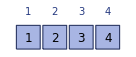
{-Graphics-,-Graphics-}

```mathematica
{ArrayGraphics[{1, 2, 3, 4}], ArrayGraphics[{{1, 2, 3}, {4, 5, 6}}]}
```

The row and column indices are written outside the cells, so that a picture can be read off against the entry it names:

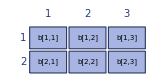

```mathematica
ArrayGraphics[GenerateSymbolicArray[b, {2, 3}]]
```

Design note.  The cells of a grid are sized to the widest entry rather than to a fixed width. A symbolic array's entries read b[1, 2] and would otherwise overflow one another. They are drawn in StandardForm, not the TraditionalForm that Graphics uses by default, which would print b[1, 2] as b(1, 2) — something the array does not contain and that could not be typed back in.

Only those two orders have a flat picture of their own. Everything above them is drawn as a nesting: a 3-array is a row of matrices, the first index choosing the matrix, which is the familiar reading.

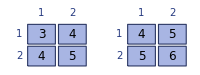

```mathematica
ArrayGraphics[Array[#1 + #2 + #3 &, {2, 2, 2}]]
```

A 4-array is a grid of grids:

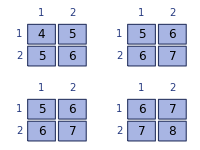

```mathematica
ArrayGraphics[Array[#1 + #2 + #3 + #4 &, {2, 2, 2, 2}]]
```

Which indices go outside and which inside is a choice, not a fact about the array. The same 3-array read the other way round, as a matrix of rows:

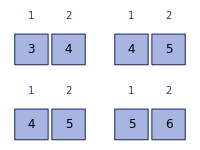

```mathematica
ArrayGraphics[Array[#1 + #2 + #3 &, {2, 2, 2}], "Nesting" -> {2, 1}]
```

Design note.  "Nesting" is a list of block sizes summing to the order of the array. In the flat family each block is one or two, since a plane picture holds no more; the first block is the outer picture and each block after it is drawn inside the cells of the one before. A block of three is refused rather than quietly turned into a lattice: this family draws plane graphics and nothing else.

```mathematica
Quiet @ ArrayGraphics[Array[1 &, {2, 2, 2}], "Nesting" -> {3}]
```

$Failed

The default splitting takes blocks of two with any remainder off the front, which is what ArrayNesting reports:

```mathematica
Table[ArrayNesting[n], {n, 0, 8}]
```

{{},{1},{2},{1,2},{2,2},{1,2,2},{2,2,2},{1,2,2,2},{2,2,2,2}}

### The spatial family: ArrayGraphics3D

The same arrays, as cubes arranged in space. At order one a line of cubes, at order two a plane of them:

```mathematica
{ArrayGraphics3D[{1, 2, 3, 4}], ArrayGraphics3D[{{1, 2, 3}, {4, 5, 6}}]}
```

{-Graphics3D-,-Graphics3D-}

At order three, the full lattice. The entry at (i, j, k) sits at the point {i, j, k}, and a gnomon in the near corner says which way the three indices run:

```mathematica
ArrayGraphics3D[Array[#1 + #2 + #3 &, {3, 3, 3}]]
```

-Graphics3D-

Design note.  The cubes have translucent faces and no outline. An outline on every cube of a lattice reads as a mesh rather than as a set of cells, and the entries behind the nearer faces can be read through them as it is. The reference implementation this package grew out of drew only this one order, and called such a picture a cubix; the name has not been kept, but the look of it has.

Colouring the indices makes the correspondence explicit, each axis taking a colour of its own:

```mathematica
ArrayGraphics3D[Array[#1 #2 #3 &, {2, 2, 2}], "Indices" -> "Colored"]
```

-Graphics3D-

### Above order three: tiling rather than nesting

Space runs out at three indices just as the plane runs out at two. But where the flat family insets a picture into each cell, the spatial family has nowhere to inset anything: a Graphics3D cannot hold another Graphics3D. So the blocks are tiled instead. A 4-array is a line of lattices, shifted along by the extent of one and a gap:

```mathematica
ArrayGraphics3D[Array[#1 + #2 + #3 + #4 &, {2, 2, 2, 2}]]
```

-Graphics3D-

A 5-array is a plane of them:

```mathematica
ArrayGraphics3D[Array[Mod[#1 + #2 + #3 + #4 + #5, 7] &, {2, 2, 2, 2, 2}]]
```

-Graphics3D-

Design note.  Everything ends up in one picture, which is the point: a tiled lattice can be turned and looked at as a single object, where a grid of separate 3D panes could not be. The spatial default takes blocks of three with any remainder off the front — ArrayNesting[n, 3] — and a block of four is refused, space holding only three indices at a time.

```mathematica
Table[ArrayNesting[n, 3], {n, 0, 8}]
```

{{},{1},{2},{3},{1,3},{2,3},{3,3},{1,3,3},{2,3,3}}

The splitting may be given here too. The same 4-array with the single index innermost instead, so that each cube of a lattice becomes a short line of cubes:

```mathematica
ArrayGraphics3D[Array[#1 + #2 + #3 + #4 &, {2, 2, 2, 2}], "Nesting" -> {3, 1}]
```

-Graphics3D-

### Options, and hypermatrices

The options are shared between the families. The cells may be left undrawn, the indices dropped, and the whole thing put on a dark ground:

```mathematica
{ArrayGraphics[{{1, 2}, {3, 4}}, "Framed" -> False],
  ArrayGraphics[{{1, 2}, {3, 4}}, "Indices" -> None],
  ArrayGraphics[{{1, 2}, {3, 4}}, "PlotTheme" -> "Dark"]}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayGraphics3D[Array[#1 + #2 + #3 &, {2, 2, 2}], "PlotTheme" -> "Dark"]
```

-Graphics3D-

Design note.  An array of more than a few hundred entries is refused rather than drawn, with ArrayGraphics::big. A picture of a thousand cells is not a picture of anything; "MaxEntries" raises the limit for anyone who disagrees.

```mathematica
Quiet @ ArrayGraphics[Array[1 &, {12, 12, 12}]]
```

$Failed

A hypermatrix draws each of its arrays, in its own canonical order, in either family:

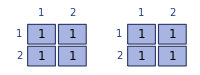
-Graphics--Graphics--Graphics-

```mathematica
HypermatrixGraphics @ Hypermatrix[{{1, 2, 3}, {{1, 2}, {3, 4}}, Array[1 &, {2, 2, 2}]}]
```

```mathematica
HypermatrixGraphics3D @ Hypermatrix[{{1, 2, 3}, {{1, 2}, {3, 4}}, Array[1 &, {2, 2, 2}]}]
```

-Graphics3D--Graphics3D--Graphics3D-

## 6. Special arrays

The constant arrays and the generalized Kronecker deltas are available in any order, dimension and value domain. Each declares the strongest symmetry that actually holds of it, which the ArrayObject constructor then verifies.

```mathematica
{Normal @ ZeroArray[2, 3], Normal @ OneArray[2, 3]}
```

{{{0,0,0},{0,0,0},{0,0,0}},{{1,1,1},{1,1,1},{1,1,1}}}

The identity array is one where all of its indices agree. At order two it is the identity matrix; at order three it is one only on the main diagonal:

```mathematica
{Normal @ IdentityArray[2, 3], Normal @ IdentityArray[3, 2]}
```

{{{1,0,0},{0,1,0},{0,0,1}},{{{1,0},{0,0}},{{0,0},{0,1}}}}

A partial identity is one where the indices at chosen positions agree, whatever the others do. These are the three partial identities of a 3-array, one per pair of indices:

```mathematica
Normal @ PartialIdentityArray[3, 2, #] & /@ {{1, 2}, {2, 3}, {1, 3}}
```

{{{{1,1},{0,0}},{{0,0},{1,1}}},{{{1,0},{0,1}},{{1,0},{0,1}}},{{{1,0},{1,0}},{{0,1},{0,1}}}}

Design note.  A constant array and a full identity are invariant under every permutation of their indices, so they are declared symmetric. A partial identity on only some positions is not, so it is declared rigid. Naming every position gives back the full identity exactly.

```mathematica
{ArraySymmetry @ ZeroArray[3, 2], ArraySymmetry @ IdentityArray[3, 2],
  ArraySymmetry @ PartialIdentityArray[3, 2, {1, 2}],
  PartialIdentityArray[3, 2, {1, 2, 3}] === IdentityArray[3, 2]}
```

{Symmetric,Symmetric,Rigid,True}

### Seeing them

These arrays are the ones whose shape is worth looking at, since what makes each of them special is where its entries sit rather than what they are. Both families of pictures are useful here, and at different orders.

A constant array says the same thing at every position, whatever its dimensions. Order one, order two, and a rectangular one that is not regular at all:

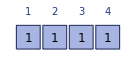
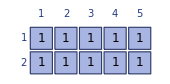
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{ArrayGraphics @ OneArray[{4}], ArrayGraphics @ ZeroArray[2, 3],
  ArrayGraphics @ OneArray[{2, 5}]}
```

The identity matrix, and beside it the same thing one order up, where the ones sit on the main diagonal of the cube:

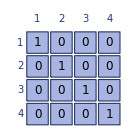
{-Graphics-,-Graphics3D-}

```mathematica
{ArrayGraphics @ IdentityArray[2, 4], ArrayGraphics3D @ IdentityArray[3, 3]}
```

Design note.  At order three the flat picture and the spatial one say different things about the same array. Flat, the identity is a row of matrices, each with a single one in it, marching down the diagonal as the first index advances. In space it is the diagonal itself, which is the thing the array is actually named after.

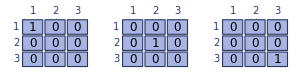

```mathematica
ArrayGraphics @ IdentityArray[3, 3]
```

A partial identity is one where the indices at chosen positions agree, whatever the others do. Each of the three is a plane through the cube, and which plane it is depends on the pair:

```mathematica
ArrayGraphics3D @ PartialIdentityArray[3, 3, #] & /@ {{1, 2}, {2, 3}, {1, 3}}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

Design note.  The picture is the argument for the name. Where the full identity picks out a line through the cube, a partial identity picks out a plane — and the three of them, one per pair of indices, are three planes meeting along that line. Naming every position leaves only the line, which is the full identity again.

Dimension by dimension, the identity at order three grows as a diagonal should:

```mathematica
ArrayGraphics3D @ IdentityArray[3, #] & /@ {2, 3, 4}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

The domains show up too. Over the two-element field the identity matrix has the same shape, with entries of that field rather than integers:

```mathematica
ArrayGraphics @ IdentityArray[2, 3, FiniteField[2, 1]]
```

-Graphics-

## 7. Contraction

ArrayMultiply contracts a list of arrays according to an index specification, in the manner of Einstein summation. Indices named in the output survive; the rest are summed over.

```mathematica
a = {{1, 2}, {3, 4}}; b = {{0, 1}, {1, 0}};
ArrayMultiply[{a, b}, "ij,jk->ik"]
```

ArrayObject[…]

The specification may equally be given as a rule between lists of index labels:

```mathematica
{Normal @ ArrayMultiply[{a, b}, "ij,jk->ik"],
  Normal @ ArrayMultiply[{a, b}, {{1, 2}, {2, 3}} -> {1, 3}]}
```

{{{2,1},{4,3}},{{2,1},{4,3}}}

Repeating an index within one array takes a diagonal, and leaving it out of the output sums it, so a trace and a transpose are contractions too:

```mathematica
{Normal @ ArrayMultiply[{a}, "ii->i"], Normal @ ArrayMultiply[{a}, "ii->"],
  Normal @ ArrayMultiply[{a}, "ij->ji"]}
```

{{1,4},5,{{1,3},{2,4}}}

Design note.  An index may occur in any number of the arrays at once, and may occur in the output as well as in the inputs. That is what lets a single specification express the three-way contractions of the ternary products, which no sequence of pairwise contractions would give.

The Bhattacharya-Mesner product of three 3-arrays joins all three on one index:

```mathematica
x = Array[#1 + #2 + #3 &, {2, 2, 2}];
Normal @ ArrayMultiply[{x, x, x}, "ijp,ipk,pjk->ijk"]
```

{{{91,148},{148,230}},{{148,230},{230,341}}}

Design note.  The result comes back as an array object, whatever the entries turned out to be. Contracting every index away leaves a single entry, which is the array of order zero, and Normal of that gives the scalar itself. There is nothing here to decide: an array of arbitrary expressions is an array like any other, which is the whole point of there being one array object.

The other side of the same coin: an array of order zero is named in a specification by an empty group of index labels, which is how a scalar enters a contraction.

```mathematica
Normal @ ArrayMultiply[{3, a}, ",ij->ij"]
```

{{3,6},{9,12}}

### Numerical and symbolic arrays

A symbolic array is a list of lists of terms with explicit indices, and a contraction of symbolic arrays simply builds the corresponding expressions in a list of lists. The symbols behave as Wolfram Language symbols always do, which is to say as complex variables:

```mathematica
sa = Normal @ GenerateSymbolicArray[p, {2, 2}];
sb = Normal @ GenerateSymbolicArray[q, {2, 2}];
{sa, sb}
```

{{{p[1,1],p[1,2]},{p[2,1],p[2,2]}},{{q[1,1],q[1,2]},{q[2,1],q[2,2]}}}

```mathematica
ArrayMultiply[{sa, sb}, "ij,jk->ik"]
```

ArrayObject[…]

It agrees with the built-in matrix product, as it should:

```mathematica
ArrayMultiply[{sa, sb}, "ij,jk->ik"] === sa . sb
```

False

Design note.  Arrays with numeric entries and arrays with generated ones may be contracted together. That was once refused, on the grounds that the result would be neither kind of object; with one array object the objection has nothing left to stand on, and the entries of the result are simply the expressions the contraction builds.

```mathematica
Normal @ ArrayMultiply[{{{1, 2}, {3, 4}}, sb}, "ij,jk->ik"]
```

{{q[1,1]+2 q[2,1],q[1,2]+2 q[2,2]},{3 q[1,1]+4 q[2,1],3 q[1,2]+4 q[2,2]}}

### Contracting every index: the trace

An operation need not return an array. Contracting a single matrix onto no indices at all sums its diagonal, which is the trace, and works on numerical and symbolic entries alike:

```mathematica
trace[u_List] := Normal @ ArrayMultiply[{u}, "pp->"];
{trace[{{1, 2}, {3, 4}}], trace[sa]}
```

{5,p[1,1]+p[2,2]}

```mathematica
{trace[{{1, 2}, {3, 4}}] === Tr[{{1, 2}, {3, 4}}], trace[sa] === Tr[sa]}
```

{True,True}

Design note.  The Normal is doing something here. A contraction onto no indices gives back the 0-array rather than a bare number, and Normal takes its single entry. It does the same whatever the entries were, so the one definition covers every case.

## 8. Adding and multiplying entry by entry

Contraction is one of the two things one does with arrays. The other is to combine them entry by entry, which is what makes arrays of a given shape a vector space rather than merely a collection of tables. ArrayAdd and ArrayTimes do that:

```mathematica
u = {{1, 2}, {3, 4}}; v = {{5, 6}, {7, 8}};
{Normal @ ArrayAdd[u, v], Normal @ ArrayTimes[u, v]}
```

{{{6,8},{10,12}},{{5,12},{21,32}}}

Plus and Times on array objects are those same operations, so arrays may be combined in ordinary arithmetic notation:

```mathematica
{Normal[ArrayObject[u] + ArrayObject[v]],
  Normal[ArrayObject[u] - ArrayObject[v]],
  Normal[ArrayObject[u] ArrayObject[v]]}
```

{{{6,8},{10,12}},{{-4,-4},{-4,-4}},{{5,12},{21,32}}}

An array of order zero has no shape of its own, so it combines with an array of any dimensions, reaching every entry:

```mathematica
{Normal @ ArrayTimes[2, u], Normal @ ArrayAdd[1, u]}
```

{{{2,4},{6,8}},{{2,3},{4,5}}}

Design note.  This is why scalar multiplication needs no name of its own. A scalar is the 0-array; multiplying an array by one is the same entry-by-entry multiplication as multiplying it by another array of its own shape, with the single entry spread over the whole shape rather than matched index for index. One operation, one rule, and 2 a is ArrayTimes[ArrayObject[2], a] written shorter.

```mathematica
ArrayTimes[2, u] === ArrayTimes[ArrayObject[2], u]
```

True

Arrays of different dimensions cannot be combined this way, and are refused rather than padded or truncated:

```mathematica
Quiet @ ArrayAdd[{1, 2}, {1, 2, 3}]
```

$Failed

Design note.  Entries of any kind may be combined, a number meeting an expression having the obvious meaning, and the result is an array object like anything else here. ArrayMultiply once refused the same mixture and no longer does, for the same reason: with one array object there is nothing ambiguous about what comes back.

```mathematica
{2 GenerateSymbolicArray[c, {2}], ArrayObject[{1, 2}] + GenerateSymbolicArray[c, {2}]}
```

{ArrayObject[…],ArrayObject[…]}

A symmetry that every argument declares is carried over to the result, since an entry-by-entry operation treats each index tuple separately. Where the arguments disagree nothing is claimed:

```mathematica
{ArraySymmetry @ ArrayAdd[ArrayObject[{{1, 2}, {2, 3}}, "Symmetric"],
                           ArrayObject[{{0, 1}, {1, 0}}, "Symmetric"]],
  ArraySymmetry @ ArrayAdd[ArrayObject[{{1, 2}, {2, 3}}, "Symmetric"],
                           ArrayObject[u]]}
```

{Symmetric,Rigid}

Design note.  The arguments are given directly rather than in a list, unlike ArrayMultiply, which takes a list of arrays and a specification alongside it. A list of arrays is itself an array, so ArrayAdd[{v1, v2}] would be ambiguous: it could be the sum of two vectors or the matrix they form. Given directly there is nothing to guess.

## 9. Searching for equational identities

FindArrayEquations takes a list of array operations and a list of generic arguments, forms every way of nesting the operations over those arguments, and returns the equations that hold between them. Operations are ordinary functions of arrays, so they are easily built out of ArrayMultiply:

```mathematica
dot[u_List, w_List] := Normal @ ArrayMultiply[{u, w}, "ij,jk->ik"];
Fish[u_List, w_List, t_List] := Normal @ ArrayMultiply[{u, w, t}, "ijp,qrp,qrk->ijk"];
BM[u_List, w_List, t_List] := Normal @ ArrayMultiply[{u, w, t}, "ijp,ipk,pjk->ijk"];
```

Ordinary matrix multiplication on three generic arguments finds associativity, and nothing else:

```mathematica
FindArrayEquations[{dot}, {a1, a2, a3}, "Order" -> 2, "Dimension" -> 3]
```

{dot[a1,dot[a2,a3]]==dot[dot[a1,a2],a3]}

The Fish product on five generic arguments finds a twisted form of ternary associativity. One of the two equations below is plain associativity in the outer arguments; the other reverses the inner three:

```mathematica
FindArrayEquations[{Fish}, {a1, a2, a3, a4, a5}]
```

{Fish[a1,a2,Fish[a3,a4,a5]]==Fish[a1,Fish[a4,a3,a2],a5],Fish[a1,a2,Fish[a3,a4,a5]]==Fish[Fish[a1,a2,a3],a4,a5]}

The Bhattacharya-Mesner product, on the same five arguments, satisfies nothing at all:

```mathematica
FindArrayEquations[{BM}, {a1, a2, a3, a4, a5}]
```

{}

Design note.  The search is in two stages, and that is what makes it quick. Every term is first evaluated on random integer arrays and only pairs that agree there are carried forward. Two terms equal as identities agree on any arrays, so nothing correct is ever thrown away; the numerical stage only proposes, and the symbolic stage disposes. The surviving candidates are then checked on symbolic arrays by expanding the difference of the two sides, which is exact for polynomials and far quicker than a general simplification.

Whether the arguments may be permuted is an option. With a fixed order only the nesting varies, which for matrix multiplication makes no difference, since associativity does not move its arguments:

```mathematica
FindArrayEquations[{dot}, {a1, a2, a3}, "Order" -> 2, "Dimension" -> 3,
                    "Permute" -> False]
```

{dot[a1,dot[a2,a3]]==dot[dot[a1,a2],a3]}

Design note.  An identity verified on symbolic arrays of a given dimension is proved at that dimension, not at every dimension. The default is 2, which is small and quick; raising "Dimension" checks more widely. The Fish equations above come out the same at dimension 3, which is reassuring without being a proof in general.

### More than one operation at a time

Operations of different arities may be searched together. A transpose is unary and a matrix product binary; on two generic arguments they give the law that transposing a product reverses it, and the law that transposing twice does nothing:

```mathematica
perp[u_List] := Normal @ ArrayMultiply[{u}, "ij->ji"];
FindArrayEquations[{perp, dot}, {a1, a2}]
```

{a1==perp[perp[a1]],dot[perp[a1],perp[a2]]==perp[dot[a2,a1]]}

Design note.  An operation of arity one is the exception to the rule that a term uses exactly the given arguments. It takes a term to a term of the same shape, so it may be applied over and over at any point without consuming an argument, and every term is offered wrapped in up to "UnaryDepth" nested unary operations, two by default. That is what brings the involutivity within reach: it needs the transpose twice over on one argument, where the anti-homomorphism law uses it once on each side.

Setting the depth to one puts the involutivity back out of reach — and with it gone, the remaining law is reported in each of its forms instead of once, since without perp[perp[a]] == a there is nothing to rewrite one form into another:

```mathematica
FindArrayEquations[{perp, dot}, {a1, a2}, "UnaryDepth" -> 1]
```

{dot[perp[a1],perp[a2]]==perp[dot[a2,a1]],dot[a1,perp[a2]]==perp[dot[a2,perp[a1]]],dot[a2,perp[a1]]==perp[dot[a1,perp[a2]]],dot[perp[a1],a2]==perp[dot[perp[a2],a1]],dot[perp[a2],a1]==perp[dot[perp[a1],a2]],dot[a1,a2]==perp[dot[perp[a2],perp[a1]]],dot[a2,a1]==perp[dot[perp[a1],perp[a2]]]}

The anti-homomorphism law moves its arguments, so holding them in the order given leaves only the involutivity, which does not:

```mathematica
FindArrayEquations[{perp, dot}, {a1, a2}, "Permute" -> False]
```

{a1==perp[perp[a1]]}

Design note.  Freely nested unary operations bring a flood with them. Every consequence of those two laws is an equation between terms of the search, and each would be reported in its own right: a hundred and more of them here, all saying the same two things over again. So an equation that follows from the others is left out. Each equation is read as a schema, its arguments standing for arbitrary terms, and turned into a rewrite rule that fires only when it makes a term strictly smaller; any number of such rules is then a terminating rewriting system, and an equation whose two sides rewrite to a common form is a consequence of the ones already kept. "Reduce" -> False reports everything found.

```mathematica
Length @ FindArrayEquations[{perp, dot}, {a1, a2}, "Reduce" -> False]
```

115

Design note.  What survives is a basis, not a canonical set. Which of several equivalent forms of a law is kept depends on the order the equations are considered in — the anti-homomorphism law above is reported with the transposes gathered on whichever side the ordering favours — and the reduction is by rewriting alone, so a consequence that rewriting cannot reach is still reported. A genuinely minimal set of axioms is the business of Knuth-Bendix completion, which this is not.

A trace and a matrix product give the cyclic property of the trace:

```mathematica
FindArrayEquations[{trace, dot}, {a1, a2}]
```

{trace[dot[a1,a2]]==trace[dot[a2,a1]]}

Design note.  The trace returns a scalar, so a nesting that feeds it back into a product cannot evaluate. Such a term is dropped rather than compared, which is what lets an operation of that shape sit at the top of a term without having to be excluded by hand.

Design note.  Neither of those searches was told the shape of its test arrays. With "Order" -> Automatic, the default, the smallest order on which every operation actually evaluates is used, which is 2 for matrix operations and 3 for the ternary array products. Operations are shape-specific enough that this is a search for the shape they are defined on rather than a guess.

Forcing a shape the operations cannot take says so, rather than coming back empty:

```mathematica
Quiet @ FindArrayEquations[{perp, dot}, {a1, a2}, "Order" -> 4]
```

$Failed

Design note.  An empty result and a result that could not be computed are different answers, and conflating them would be the worst kind of quiet failure: it would read as a proof that no identity exists. Whenever no nesting evaluates, FindArrayEquations::eval is issued and $Failed returned.

## 10. The adjacency hypermatrix

The two halves of the package meet here. A hypergraph is a multiset of edges, each with an arity and a symmetry type; an array has an order and a symmetry. The two vocabularies line up one for one, and the passage from a hypergraph to a hypermatrix is what that correspondence looks like when it is written down.

```mathematica
hAdj = Hypergraph[{Edge[{1, 2, 3}, "Unordered"], Edge[{3, 4}, "Directed"],
                   Edge[{1, 2}, "Directed"]}]
```

-Graphics-

```mathematica
hmAdj = AdjacencyHypermatrix[hAdj];
{hmAdj["Orders"], hmAdj["Dimensions"], hmAdj["Symmetries"]}
```

{{2,3},{{4,4},{4,4,4}},{Rigid,Symmetric}}

Design note.  An edge of arity k gives an array of order k, and an edge symmetry gives an array symmetry: directed to rigid, cyclic to cyclic, unordered to symmetric. An array holds one symmetry and one order, so the edges are gathered by arity and symmetry type together, and each group becomes one array. A Hypermatrix then sorts those arrays by order, then dimensions, then symmetry — which is exactly what the grouping was keyed on, so the result comes out sorted by the very thing that distinguishes its parts.

The two directed edges land where they are, in a rigid matrix whose indices run over the vertices in the order VertexList gives them:

```mathematica
MatrixForm @ Normal @ First @ HypermatrixArrays[hmAdj]
```

(0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0)

The unordered edge fills the whole orbit of its three vertices, all six permutations, which is what makes that array symmetric:

```mathematica
Position[Normal @ Last @ HypermatrixArrays[hmAdj], 1]
```

{{1,2,3},{1,3,2},{2,1,3},{2,3,1},{3,1,2},{3,2,1}}

A cyclic edge fills the three rotations, and a directed one the single tuple:

```mathematica
{Position[Normal @ First @ HypermatrixArrays @
     AdjacencyHypermatrix @ Hypergraph[{Edge[{1, 2, 3}, "Cyclic"]}], 1],
  Position[Normal @ First @ HypermatrixArrays @
     AdjacencyHypermatrix @ Hypergraph[{Edge[{1, 2, 3}, "Directed"]}], 1]}
```

{{{1,2,3},{2,3,1},{3,1,2}},{{1,2,3}}}

Design note.  The entry is looked up against the canonical index of its tuple — the least one in its orbit under the symmetry, the same arrayCanonicalIndex by which a symbolic array decides which of its entries are the same entry. Every tuple of an orbit therefore reads the same count, and the array carries its declared symmetry by construction rather than by luck. That is the whole trick, and it is why the two definitions had to agree in the first place.

Edges of one arity but different symmetry types cannot share an array, so they do not:

```mathematica
AdjacencyHypermatrix[Hypergraph[{Edge[{1, 2}, "Directed"], Edge[{1, 2}, "Unordered"],
                                  Edge[{1, 2}, "Cyclic"]}]]["Symmetries"]
```

{Symmetric,Cyclic,Rigid}

A hypergraph is a multiset, so a repeated edge counts twice:

```mathematica
Normal @ First @ HypermatrixArrays @
  AdjacencyHypermatrix @ Hypergraph[{Edge[{1, 2}], Edge[{1, 2}], Edge[{2, 1}]}]
```

{{0,2},{1,0}}

Design note.  Nothing is lost in the passage. Reading every canonical entry back out names exactly the edges that went in, with their multiplicities, which the test file checks on three hundred random hypergraphs. Labels are the one thing that does not survive: this is the adjacency of the skeleton, and a labelled hypergraph gives the same hypermatrix as HypergraphSkeleton of it.

Being ordinary arrays, they draw like ordinary arrays:

```mathematica
HypermatrixGraphics @ AdjacencyHypermatrix @
  Hypergraph[{Edge[{1, 2}, "Directed"], Edge[{2, 3}, "Directed"], Edge[{1, 3}, "Directed"]}]
```

-Graphics-

And an unordered edge of arity three, seen as the lattice it is:

```mathematica
ArrayGraphics3D @ First @ HypermatrixArrays @
  AdjacencyHypermatrix @ Hypergraph[{Edge[{1, 2, 3}, "Unordered"]}]
```

-Graphics3D-

### Multiplicities

A hypergraph is a multiset of edges, and identical copies of an edge all want the same entry. They get it, and the entry counts them:

```mathematica
Normal @ First @ HypermatrixArrays @ AdjacencyHypermatrix @
  Hypergraph[{Edge[{1, 2}], Edge[{1, 2}], Edge[{2, 1}]}]
```

{{0,2},{1,0}}

That holds at every symmetry type, over the whole orbit each time. Three copies of an unordered edge put a 3 at each of its six permutations; two copies of a cyclic one put a 2 at each of its three rotations:

```mathematica
{Union @ Cases[Normal @ First @ HypermatrixArrays @ AdjacencyHypermatrix @
      Hypergraph[Table[Edge[{1, 2, 3}, "Unordered"], 3]], _?Positive, Infinity],
  Union @ Cases[Normal @ First @ HypermatrixArrays @ AdjacencyHypermatrix @
      Hypergraph[Table[Edge[{1, 2, 3}, "Cyclic"], 2]], _?Positive, Infinity]}
```

{{3},{2}}

Design note.  Edges are stored with their vertices in the canonical order of their symmetry type, so two spellings of one unordered edge are one edge written twice, not two edges. The entry is 2, as it should be.

```mathematica
Normal @ First @ HypermatrixArrays @ AdjacencyHypermatrix @
  Hypergraph[{Edge[{1, 2}, "Unordered"], Edge[{2, 1}, "Unordered"]}]
```

{{0,2},{2,0}}

### Labels as entries

If the edges carry labels, those labels can be the entries instead of the counts. With "Labeled" -> True the entry at a position is the label of the edge that sits there, and 0 where no edge does:

```mathematica
hLab = Hypergraph[{Edge[{1, 2}, "Directed", "a"], Edge[{2, 3}, "Directed", "b"],
                   Edge[{1, 2, 3}, "Unordered", "c"]}];
Normal @ First @ HypermatrixArrays @ AdjacencyHypermatrix[hLab, "Labeled" -> True]
```

{{0,a,0},{0,0,b},{0,0,0}}

A label fills the whole orbit of its edge, exactly as a count does, so the arrays carry their symmetries just the same. The unordered edge labelled c appears at all six permutations of its vertices:

```mathematica
{Length @ Position[Normal @ Last @ HypermatrixArrays @
      AdjacencyHypermatrix[hLab, "Labeled" -> True], "c"],
  ArraySymmetry @ Last @ HypermatrixArrays @ AdjacencyHypermatrix[hLab, "Labeled" -> True]}
```

{6,Symmetric}

Design note.  The value domain of such an array is "Label". It is the one domain that is never inferred: its test admits anything at all, so were it in the list that inference walks, every array whose entries fitted nothing else would quietly become an array of labels. It has to be asked for, which is what "Labeled" -> True does.

```mathematica
{AdjacencyHypermatrix[hLab]["Domains"],
  AdjacencyHypermatrix[hLab, "Labeled" -> True]["Domains"]}
```

{{Integer,Integer},{Expression,Expression}}

Counting remains what happens by default, so nothing changes for a hypergraph whose labels are beside the point:

```mathematica
AdjacencyHypermatrix[hLab] === AdjacencyHypermatrix[hLab, "Labeled" -> False]
```

True

### Why labels need a simple hypergraph

An entry can hold a count of any size, but it cannot hold two labels. So labels can only be the entries when no two edges want the same one — which is exactly what it means for the hypergraph to be simple. SimpleHypergraphQ tests for it:

```mathematica
{SimpleHypergraphQ[hLab],
  SimpleHypergraphQ @ Hypergraph[{Edge[{1, 2}, "Directed", "a"],
                                  Edge[{1, 2}, "Directed", "b"]}]}
```

{True,False}

The second is two edges in one place. Counting them is no trouble; labelling them is refused:

```mathematica
Quiet @ AdjacencyHypermatrix[
  Hypergraph[{Edge[{1, 2}, "Directed", "a"], Edge[{1, 2}, "Directed", "b"]}],
  "Labeled" -> True]
```

$Failed

```mathematica
Normal @ First @ HypermatrixArrays @ AdjacencyHypermatrix @
  Hypergraph[{Edge[{1, 2}, "Directed", "a"], Edge[{1, 2}, "Directed", "b"]}]
```

{{0,2},{0,0}}

Design note.  Simplicity is tested on the skeleton, which is the right place: two edges differing only by a label are the same edge of the same skeleton, and it is their sharing a position that matters, not their having different labels. A vertex repeated within one edge, by contrast, is allowed — that is a property of one edge rather than a collision between two, and it obstructs nothing.

```mathematica
{SimpleHypergraphQ @ Hypergraph[{Edge[{1, 1, 2}, "Unordered"]}],
  Union @ Flatten @ Normal @ First @ HypermatrixArrays @ AdjacencyHypermatrix[
     Hypergraph[{Edge[{1, 1, 2}, "Unordered", "r"]}], "Labeled" -> True]}
```

{True,{0,r}}

Edges of one arity but different symmetry types go to different arrays, so they never collide and a hypergraph holding both is simple:

```mathematica
AdjacencyHypermatrix[
  Hypergraph[{Edge[{1, 2}, "Directed", "d"], Edge[{1, 2}, "Unordered", "u"]}],
  "Labeled" -> True]["Symmetries"]
```

{Symmetric,Rigid}

Design note.  Vertex labels have no slot here. An entry of an adjacency array answers to an edge, so edge labels are what can go in it; the vertices are the indices rather than the entries, and their labels stay in VertexList. An edge carrying no label of its own gives None, which is not the same as the 0 that means no edge at all.

```mathematica
Normal @ First @ HypermatrixArrays @ AdjacencyHypermatrix[
  Hypergraph[{Edge[{1, 2}, "Directed", "a"], Edge[{2, 1}, "Directed"]}], "Labeled" -> True]
```

{{0,a},{None,0}}

### Which order do the indices run in?

The vertices of a hypergraph are a set. They have no order of their own, and yet the indices of an array are numbered one to n. Something must be choosing, and it is worth being clear about what.

The choice is made by the Hypergraph constructor, not by AdjacencyHypermatrix. A hypergraph is stored with its vertices sorted, so the order is a property of the object rather than of how it was typed. Giving the same edges in a different order changes nothing:

```mathematica
hOrdA = Hypergraph[{Edge[{3, 1}], Edge[{2, 3}]}];
hOrdB = Hypergraph[{Edge[{2, 3}], Edge[{3, 1}]}];
{VertexID /@ VertexList[hOrdA], hOrdA === hOrdB,
  AdjacencyHypermatrix[hOrdA] === AdjacencyHypermatrix[hOrdB]}
```

{{1,2,3},True,True}

So far so good. But the sort is on the vertex identifiers, and identifiers are whatever the user chose them to be. Here are two isomorphic hypergraphs — the same path on three vertices — whose vertices are named differently:

```mathematica
hNum = Hypergraph[{Edge[{1, 2}], Edge[{2, 3}]}];
hStr = Hypergraph[{Edge[{"z", "a"}], Edge[{"a", "m"}]}];
{IsomorphicHypergraphQ[hNum, hStr],
  VertexID /@ VertexList[hNum], VertexID /@ VertexList[hStr]}
```

{True,{1,2,3},{a,m,z}}

Sorting puts a before m before z, so the vertex called z — the start of the path — ends up third. The two adjacency matrices are not equal:

```mathematica
mNum = Normal @ First @ HypermatrixArrays @ AdjacencyHypermatrix[hNum];
mStr = Normal @ First @ HypermatrixArrays @ AdjacencyHypermatrix[hStr];
{MatrixForm[mNum], MatrixForm[mStr], mNum === mStr}
```

{(0 | 1 | 0
0 | 0 | 1
0 | 0 | 0),(0 | 1 | 0
0 | 0 | 0
1 | 0 | 0),False}

Design note.  This is the honest answer to the question: there is a choice, and renaming the vertices can change the hypermatrix. What the sort buys is not that the choice goes away but that it is made the same way every time. AdjacencyHypermatrix is a function of the hypergraph it is given, with nothing arbitrary left in it; what it is not is a function of the isomorphism class.

The two matrices are of course related, by the permutation the renaming induces on the indices. Old vertex 1 is called z, which sorts third; 2 is called a, which sorts first; 3 is called m, which sorts second:

```mathematica
perm = {3, 1, 2};
mNum[[InversePermutation[perm], InversePermutation[perm]]] === mStr
```

True

The same permutation, applied in every index slot at once, relates the higher-order arrays too. Simultaneous, because one vertex set is being renumbered, not three:

```mathematica
gNum = Hypergraph[{Edge[{1, 2, 3}, "Unordered"], Edge[{1, 1, 2}, "Unordered"]}];
gStr = Hypergraph[{Edge[{"z", "a", "m"}, "Unordered"], Edge[{"z", "z", "a"}, "Unordered"]}];
aNum = Normal @ First @ HypermatrixArrays @ AdjacencyHypermatrix[gNum];
aStr = Normal @ First @ HypermatrixArrays @ AdjacencyHypermatrix[gStr];
{aNum === aStr,
 With[{q = InversePermutation[perm]}, aNum[[q, q, q]] === aStr]}
```

{False,True}

Design note.  Mathematically this is the usual state of affairs: an adjacency array is attached to a hypergraph together with a numbering of its vertices, and as an invariant of the isomorphism class it is defined only up to simultaneous permutation of its indices. Nothing here is a defect of the implementation — it is what the object is.

If what is wanted is an invariant, the package already has the missing half. CanonicalHypergraph picks a representative of the isomorphism class, relabelling the vertices one to n; composing the two gives a hypermatrix that depends on the isomorphism class alone:

```mathematica
{VertexID /@ VertexList @ CanonicalHypergraph[hNum],
  VertexID /@ VertexList @ CanonicalHypergraph[hStr],
  CanonicalHypergraph[hNum] === CanonicalHypergraph[hStr]}
```

{{1,2,3},{1,2,3},True}

```mathematica
AdjacencyHypermatrix[CanonicalHypergraph[hNum]] ===
  AdjacencyHypermatrix[CanonicalHypergraph[hStr]]
```

True

Design note.  So there are two functions here, and it is worth knowing which one is wanted. AdjacencyHypermatrix[hg] is the adjacency of the hypergraph as it stands, with its own vertex names, and is the one to use when those names mean something. AdjacencyHypermatrix[ CanonicalHypergraph[hg]] is the adjacency of its isomorphism class, and is the one to use when they do not. The second is not offered as a separate function because it is already a composition of two, and naming it would only hide which of the two was meant.

## 11. Scope and limits

A scalar is the array of order zero: no indices, no dimensions, one entry. That is what a full contraction leaves behind and what multiplies an array entry by entry, so the alternative — treating a plain value as something other than an array — would have needed a separate rule at each of those places.

Only the three symmetries named in the plan are recognized: rigid, cyclic and symmetric. Arbitrary index symmetry groups, and antisymmetry with its sign, are not implemented.

A declared symmetry is checked by testing invariance under a generating set of the group, one transposition and one rotation, rather than under every permutation. That is enough, and it keeps the check cheap for arrays of high order.

The file tests/HypermatrixExamples.wls runs the examples in this notebook as assertions, plus 1300 randomized checks: that order, dimensions and regularity always agree with the entries; that a symmetrized array is always accepted as symmetric and a cyclically symmetrized one as cyclic; that the canonical order of a hypermatrix never depends on the order its arrays were given in; and that the result really is sorted by the three stated criteria.

The file tests/ArrayAlgebraExamples.wls does the same for the special arrays, ArrayMultiply, the entry-by-entry operations and FindArrayEquations, checking the contraction against Dot, Tr, Diagonal, Transpose and Outer, and confirming that every equation reported really holds on arrays the search never saw.

Next: the graphical rendering of 1-, 2- and 3-arrays.